```mathematica
(* Computer Graphics with Applications (Google's Version) *)
```

```mathematica
(* Lecture 5. 3D Primitives. Animations *)
```

```mathematica
SetOptions[{Plot,Plot3D,DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot, Graphics , Graphics3D,SphericalPlot3D,DensityPlot,DensityPlot3D,ContourPlot,SliceContourPlot3D,SliceDensityPlot3D,RegionPlot,RegionPlot3D,Graphics3D,RevolutionPlot3D,VectorPlot,VectorPlot3D,StreamPlot,PolarPlot},ImageSize->Medium];
```

```mathematica
SetOptions[{Plot3D,ParametricPlot3D,RevolutionPlot3D},Mesh->True];
```

```mathematica
SetOptions[{Plot,ParametricPlot},Mesh->False];
```

```mathematica
(* 3D primitives *)
```

```mathematica
(* By default Mathematica draws the axes on the box. To change it use AxesOrigin->{x,y,z} *)
```

```mathematica
(* 
Example 1 Create 10 random points in the range -0.5,0.5 in x,y, and z. Plot them in 3D. Connect them by linesRandom[] generates a real random number between 0 and 1  RandomReal[range] generates a real random with the range {min,max} 
*)
```

```mathematica
Random05[]:=RandomReal[{-0.5,0.5}]
```

```mathematica
fRandom3D[]:={Random05[],Random05[],Random05[]}
```

```mathematica
P10=Table [fRandom3D[],{i,10}];
```

```mathematica
Points10=Point[P10];
```

```mathematica
Lines10=Line[P10];
```

```mathematica
GP10=Graphics3D[{{Red,PointSize->0.05,Points10},Lines10},Axes->True]
```

-Graphics3D-

```mathematica
(* The basic 3D primitives are given below. The wrapper Graphics3D[] is required. The most important primitives are Line, Point, Arrow and Polygon.
*)
```

-Graphics-

```mathematica
(* More primitives and relevant options. All this material is available in M-14 documentation. Additionally function Options[F] shows all options associated with function F.
*)
```

```mathematica
(* -Graphics-*) 
(* -Graphics-*)
```

```mathematica
(* Space curves by the 3D primitives *)
```

```mathematica
(* Define a spiral with R=3.5 and "length" L10=10*)
```

```mathematica
R=3.5;
```

```mathematica
x[t_]:=R Sin[t]
```

```mathematica
y[t_]:=R Cos[t]
```

```mathematica
z[t_]:=t (* นี่แหละทำให้มันเป็น spiral *)
```

```mathematica
S[t_]:={x[t],y[t],z[t]}
```

```mathematica
(* Define 50 points on the interval [0,10] *)
```

```mathematica
(* # of points *)
```

```mathematica
Npoints=50;
```

```mathematica
(* "Length" of the spiral L10 *)
```

```mathematica
L10=10;
```

```mathematica
P50=Table[1.0*L10/Npoints*i,{i,Npoints}]
```

{0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.,3.2,3.4,3.6,3.8,4.,4.2,4.4,4.6,4.8,5.,5.2,5.4,5.6,5.8,6.,6.2,6.4,6.6,6.8,7.,7.2,7.4,7.6,7.8,8.,8.2,8.4,8.6,8.8,9.,9.2,9.4,9.6,9.8,10.}

```mathematica
(* Generate a discrete set of points on the spiral  *)
```

```mathematica
(*-Graphics- *)
```

```mathematica
P50S=Map[S,P50]
```

{{0.695343,3.43023,0.2},{1.36296,3.22371,0.4},{1.97625,2.88867,0.6},{2.51075,2.43847,0.8},{2.94515,1.89106,1.},{3.26214,1.26825,1.2},{3.44907,0.594885,1.4},{3.49851,-0.102198,1.6},{3.40847,-0.795207,1.8},{3.18254,-1.45651,2.},{2.82974,-2.05975,2.2},{2.36412,-2.58088,2.4},{1.80425,-2.99911,2.6},{1.17246,-3.29778,2.8},{0.49392,-3.46497,3.},{-0.20431,-3.49403,3.2},{-0.894394,-3.38379,3.4},{-1.54882,-3.13865,3.6},{-2.1415,-2.76839,3.8},{-2.64881,-2.28775,4.},{-3.05052,-1.71591,4.2},{-3.33061,-1.07567,4.4},{-3.47792,-0.392534,4.6},{-3.48658,0.306246,4.8},{-3.35623,0.992818,5.},{-3.09209,1.63981,5.2},{-2.70468,2.22143,5.4},{-2.20943,2.71448,5.6},{-1.62611,3.09932,5.8},{-0.977954,3.3606,6.},{-0.290813,3.4879,6.2},{0.407922,3.47615,6.4},{1.09039,3.32581,6.6},{1.7294,3.04289,6.8},{2.29945,2.63866,7.},{2.77784,2.12923,7.2},{3.14548,1.53492,7.4},{3.38772,0.879409,7.6},{3.4949,0.188844,7.8},{3.46275,-0.50925,8.},{3.29256,-1.18704,8.2},{2.9911,-1.81751,8.4},{2.57039,-2.37552,8.6},{2.04721,-2.83883,8.8},{1.44241,-3.18896,9.},{0.780115,-3.41195,9.2},{0.086714,-3.49893,9.4},{-0.610144,-3.44641,9.6},{-1.28268,-3.25649,9.8},{-1.90407,-2.93675,10.}}

```mathematica
(* Plot   *)
```

```mathematica
Points50=Point[P50S];
```

```mathematica
Lines50=Line[P50S];
```

```mathematica
GP50S=Graphics3D[{{Red,PointSize->0.05,Points50},{Thickness[0.01],Lines50}},Axes->True,BoxRatios->1]
```

-Graphics3D-

```mathematica
(* Plot a title  attached to the last point P5OS[[Npoints]] *)
```

```mathematica
P50S[[Npoints]]
```

{-1.90407,-2.93675,10.}

```mathematica
T1=Style["My Spiral\nStaircase",Large,Bold,Blue,FontFamily->"SF Mono"]
```

My Spiral
Staircase

```mathematica
GP50ST1=Graphics3D[Text[T1,P50S[[Npoints]]],BoxRatios->1]
```

-Graphics3D-

```mathematica
Show[GP50S,GP50ST1]
```

-Graphics3D-

```mathematica
(* Polygon ,Cylinder Sphere, Cuboid, Cone, Spheroid *)
```

-Graphics-

```mathematica
(* Example 3D Triangle *)
```

```mathematica
Plist1={{1,0,0},{1,1,1},{0,0,1}}
```

{{1,0,0},{1,1,1},{0,0,1}}

```mathematica
pol1=Polygon[Plist1];
```

```mathematica
Graphics3D[{Pink,pol1},Axes->True,PlotLabel->Triangle]
```

-Graphics3D-

```mathematica
Graphics3D[{RGBColor[{10/255,132/255,255/255}],pol1},Axes->True,PlotLabel->Triangle] (* Custom RGB Color to System Blue haha*)
```

-Graphics3D-

```mathematica
(* Vertex colors mixed *)
```

```mathematica
ColorList3={Red,Green,Blue}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1]}

```mathematica
pol3=Polygon[Plist1, VertexColors->ColorList3]
```

Polygon[…]

```mathematica
Graphics3D[pol3]
```

-Graphics3D-

```mathematica
(* Cylinder Sphere, Cuboid, Cone, Spheroid *)
```

```mathematica
Graphics3D[{Blue,Cylinder[],Red,Sphere[{0,0,2},1.5],Black,Thick,Dashed,Line[{{-2,0,2},{2,0,2},{0,0,4},{-2,0,2}}],Yellow,Polygon[{{-3,-3,-2},{-3,3,-2},{3,3,-2},{3,-3,-2}}],Green,Opacity[.3],Cuboid[{-2,-2,-2},{2,2,-1}]}]
```

-Graphics3D-

```mathematica
(* These functions will be practiced at the Lab *)
```

```mathematica
(* Animations in 2D  *)
```

```mathematica
(* Animate[YourPlot[animationparameter],{animatioinparameter,pmin,pmax,step}]. AnimationRunning->False- important *)
```

```mathematica
(* Example 0 Animate fn[x_,n_]:=Sin[x/n] 
Note x is an independent variable whereas n is the animation parameter
Explanations at the lecture 
*)
```

```mathematica
fn[x_,n_]:=Sin[x/n]
```

```mathematica
Animate[Plot[fn[x,n],{x,0,2 Pi},PlotPoints->100,PlotRange->1,PlotLabel->"Animation-Sin[x/n]-n"],{n,1,10,1},AnimationRunning->False]
```

```mathematica
(* Compare. Below n is the independent variable and x is the animation parameter *)
```

```mathematica
Animate[Plot[fn[x,n],{n,0.1,2 Pi},PlotPoints->100,PlotRange->1,PlotLabel->"Animation-Sin[x/n]-x"],{x,1,10,1},AnimationRunning->False]
```

```mathematica
(* Example 1 Animate a parametric plot {Sin[(t^2+1)/n], Cos[t*n]}, {n,2,10,1}, {t,0,5} *)
```

```mathematica
(* Define a parametric curve, where the animation parameter is the second variable *)
```

```mathematica
Clear[x1,y1,S1,t,n]
```

```mathematica
x1[t_,n_]:=Sin[(t^2+1)/n]
```

```mathematica
y1[t_,n_]:=Cos[t*n]
```

```mathematica
S1[t_,n_]:={x1[t,n],y1[t,n]}
```

```mathematica
Animate[ParametricPlot[S1[t,n],{t,0,5},PlotRange->1],{n,1,5,1},AnimationRunning->False]
```

```mathematica
(* Any numerical or Boolean parameter can be used for animation. The animation below runs with a non integer step and a random color.   *)
```

```mathematica
Animate[ParametricPlot[S1[t,n],{t,0,5},PlotStyle->RandomColor[],PlotRange->1],{n,1,5,0.1},AnimationRunning->False]
```

```mathematica
(* Fixed colors *)
```

```mathematica
Color1={Red ,Green,Blue,Purple,Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[0.5, 0, 0.5],GrayLevel[0]}

```mathematica
Animate[ParametricPlot[S1[t,n],{t,0,5},PlotStyle->Color1[[n]],PlotRange->1],{n,1,5,1},AnimationRunning->False]
```

```mathematica
(* Manipulate. Does not require AnimationRunning->False, has an extended window  *)
```

```mathematica
Manipulate[ParametricPlot[S1[t,n],{t,0,5},PlotRange->1],{n,1,5,0.01}] (* Specify step ได้นะ! MAYBE MIDTERM EXAM HERE... *)
```

```mathematica
(* Manipulate with 2 animation parameters *)
```

```mathematica
Manipulate[ParametricPlot[S1[t,n],{t,0,5},PlotStyle->C],{n,1,5,0.1},{C, Color1}]
```

```mathematica
(* Dynamic title. Analyze functions ToExpression and ToString*)
```

```mathematica
ColorT={"Red" ,"Green","Blue","Purple","Black"}
```

{Red,Green,Blue,Purple,Black}

```mathematica
Manipulate[ParametricPlot[S1[t,n],{t,0,5},PlotStyle->ToExpression[C]],{n,1,5,0.1},{C,ColorT}]
```

```mathematica
(* Graphic functions G41[n], G42[n] *)
```

```mathematica
G41[n_]:=ParametricPlot[S1[t,n],{t,0,5},PlotRange->1.1]
```

```mathematica
S2[t_,n_]:=1/(t+1)
```

```mathematica
G42[n_]:=PolarPlot[n/(t+1),{t,0,12Pi},PlotRange->2.5,PlotStyle->{Red,Thick}]
```

```mathematica
Manipulate[{G41[n],G42[n]},{n,1,6,0.1}]
```

```mathematica
(* Compare *)
```

```mathematica
Manipulate[Show[G41[n],G42[n]],{n,1,6,0.1}]
```

```mathematica
(* Function as the input variable *)
```

```mathematica
fvar[f_,x_]:=f[x]
```

```mathematica
(* Function as the input variable *)
```

```mathematica
fvar[Sin,3Pi/2]
```

-1

```mathematica
fvar[Log,Exp[1]]
```

1

```mathematica
fmy[x_]:=x^2+x
```

```mathematica
fvar[fmy,4]
```

20

```mathematica
f2[x_]:=x^2
```

```mathematica
Listfun:={Sin,Cos,fmy, f2}
```

```mathematica
Plotf[i_]:=Plot[fvar[Listfun[[i]],x],{x,-1,1},PlotRange->1,PlotLabel->Listfun[[i]],LabelStyle->"Section"]
```

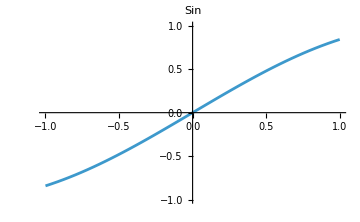

```mathematica
Plotf[1]
```

```mathematica
Manipulate[Plotf[i],{i,1,4,1}]
```

```mathematica
(* Manipulate *)
```

```mathematica
(* Animate an explicit function. a1 - amplitude, n1 -frequency, p1-shift f - parameter-function.  *)
```

```mathematica
Clear[f]
```

```mathematica
f[x_,a1_,p1_,n1_,f_]:=a1*f[n1*(x+p1)]
```

```mathematica
Manipulate[Plot[f[x,a1,p1,s1,Sin],{x,0,10},PlotRange->1],{a1,0,1},{p1,0,2Pi},{s1,1,4}]
```

```mathematica
(* Beautiful professional plots. Parametric functions *)
```

```mathematica
(* Sfxy[x_,a1_,p1_,n1_,a2_,p2_,n2_]
a1,p1,n1,a2,p2 and n2 - animation parameters *)
```

```mathematica
Sfxy[x_,a1_,p1_,n1_,a2_,p2_,n2_]:={f[x,a1,p1,n1,Sin],f[x,a2,p2,n2,Cos]}
```

```mathematica
Manipulate[ParametricPlot[Sfxy[x,a1,p1,n1,a2,p2,n2],{x,0,20 Pi},PlotRange->1,PlotPoints->200],Style["Horizontal",12,Bold],{{n1,1,"Frequency"},1,4},{{a1,1,"Amplitude"},0,1},{{p1,0,"Phase"},0,2 Pi},Delimiter,Style["Vertical",12,Bold],{{n2,5/4,"Frequency"},1,4},{{a2,1,"Amplitude"},0,1},{{p2,0,"Phase"},0,2 Pi},ControlPlacement->Left]
```

```mathematica
(* Animating 3D  *)
```

```mathematica
(* Example 0 Animate a space curve given by 
x3[u_,n_]:=n/6 u Sin[u]
  y3[u_]:=Cos[u]
  z3[u_]:=u/10, n∈[1,18] u∈[0,20] *)
```

```mathematica
x3[u_,n_]:=n/6u Sin[u]
```

```mathematica
y3[u_]:=Cos[u]
```

```mathematica
z3[u_]:=u/10
```

```mathematica
S3[u_,n_]:={x3[u,n],y3[u],z3[u]}
```

```mathematica
(* Find appropriate BoxRatios. Important! PlotRange usually must be fixed experimentally 
Note: {n,1,18} indicates that the animation step must be selected automatically(step!=1) 
In order to fix the step, it must be specified explicitly such as {n,1,18,1} 
*)
```

```mathematica
Manipulate[ParametricPlot3D[S3[u,n],{u,0,20},BoxRatios->1,PlotPoints->80,PlotRange->{{-60,60},{-1,1},{0,2}},PlotStyle->Thick,Mesh->False],{n,1,18}]
```

```mathematica
(* Example 1 Animate a growing 3D spiral with regard to dynamic range {u,0,a} where a is the animation parameter {a,1,20}. Memorize this structure  *)
```

```mathematica
x4[u_]:=Sin[u]
```

```mathematica
y4[u_]:=Cos[u]
```

```mathematica
z4[u_]:=u/10
```

```mathematica
S4[u_]:={x4[u],y4[u],z4[u]}
```

```mathematica
Manipulate[ParametricPlot3D[S4[u],{u,0,a},PlotRange->{{-1,1},{-1,1},{0,2}},PlotStyle->{Thickness[0.02], Blue}],{a,1,20}]
```

```mathematica
(* Example Animate with regard to a list of functions f[x,y] *)
```

```mathematica
Clear[Listf,x,y]
```

```mathematica
Listf={x^2+y^2,x^2-y^2, Exp[-x^2-y^2], Sin[x y],x+y}
```

{x^2+y^2,x^2-y^2,ⅇ^(-x^2-y^2),Sin[x y],x+y}

```mathematica
(* Check. *)
```

```mathematica
Plot3D[Listf[[3]],{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
(* Index solition *)
```

```mathematica
Manipulate[Plot3D[Listf[[i]],{x,-1,1},{y,-1,1},PlotStyle->Color1[[i]],Mesh->True,MeshStyle->Yellow],{i,1,Length[Listf],1}]
```

```mathematica
(* Advanced *)
```

```mathematica
(* function Position *)
```

```mathematica
Position[Listf,x^2-y^2][[1]][[1]]
```

2

```mathematica
Manipulate[Plot3D[L,{x,-1,1},{y,-1,1},PlotStyle->Color1[[Position[Listf,L][[1]][[1]]]],MeshStyle->Yellow],{L,Listf}]
```

```mathematica
(* Example Animate (x-1/R1)^2+y^2 where R1 is the animation variable changing from 1 to 20 with the step 1. Fix the PlotRange  *)
```

```mathematica
f6[x_,y_,R1_]:=(x-1/R1)^2+y^2
```

```mathematica
Manipulate[Plot3D[f6[x,y,R1],{x,-1,1},{y,-1,1},Mesh->True, PlotRange->{Automatic,Automatic,{0,5}}],{R1,1,20,1}]
```

```mathematica
(* Example Animate f7[x_,y_,n1_,n2_]:=Sin[n1*x]*Exp[-y^2*n2]  {x,-1,1} {y,-1,1} 
n1 and n2 change from 1 to 10 the  step is selected automatically  *)
```

```mathematica
f7[x_,y_,n1_,n2_]:=Sin[n1*x]*Exp[-y^2*n2]
```

```mathematica
(* Check  *)
```

```mathematica
f7[1.,1,1,1]
```

0.30956

```mathematica
Manipulate[Plot3D[f7[x,y,n1,n2],{x,-1,1} ,{y,-1,1},PlotStyle->Red,PlotRange->1],{n1,1,10},{n2,1,10}]
```

```mathematica
(* Example On one graph animate   
    an explicit surface s8[x_,y_,n_]:=n*(x^2 + y^2)/10 
and a parametric surface 
x8[u_,v_,n_]:=4 + (3 + Cos[v]) Sin[u]*n
    y8[u_,v_]:=4 + (3 + Cos[v]) Cos[u]
	z8[v_]:= 4 + Sin[v], where the animation parameter {n,1,5,0.1}
PlotPoints->40,{x,-4,4},{y,-4,4}{u,-4,4},{v,-4,4} 
*)
```

```mathematica
(* Define *)
```

```mathematica
s8[x_,y_,n_]:=n*(x^2 + y^2)/10
```

```mathematica
x8[u_,v_,n_]:=4 + (3 + Cos[v]) Sin[u]*n
```

```mathematica
y8[u_,v_]:=4 + (3 + Cos[v]) Cos[u]
```

```mathematica
z8[v_]:= 4 + Sin[v]
```

```mathematica
s8param[u_,v_,n_]:={x8[u,v,n],y8[u,v] ,z8[v]}
```

```mathematica
(* Define and check the graphics functions *)
```

```mathematica
Plot81[n_]:=Plot3D[s8[x,y,n],{x,-4,4},{y,-4,4},PlotRange -> {{-5, 5}, {-5, 5}, {0, 10}},PlotStyle->Blue,MeshStyle->White]
```

```mathematica
Plot82[n_]:=ParametricPlot3D[s8param[u,v,n],{u,-4,4},{v,-4,4},PlotRange -> {{-5, 5}, {-5, 5}, {0, 10}},PlotStyle->Red]
```

```mathematica
(* Check *)
```

```mathematica
Plot81[2]
```

-Graphics3D-

```mathematica
Plot82[3]
```

-Graphics3D-

```mathematica
(* Combined Plot-> graphic function *)
```

```mathematica
Plots8[n_]:=Show[{Plot81[n],Plot82[n]}]
```

```mathematica
(* Animation *)
```

```mathematica
Manipulate[Plots8[n],{n,1,5,0.5}]
```

```mathematica
(* Example Animate the surface of revolution with the dynamic parametric base function 
S9[t_,n_]:={Sin[t]+Sin[n t]/5,Cos[t]+Cos[n t]/5} {t,0,Pi}, the animation parameter {n,1,7,0.5}
*)
```

```mathematica
S9[t_,n_]:={Sin[t]+Sin[n t]/5,Cos[t]+Cos[n t]/5}
```

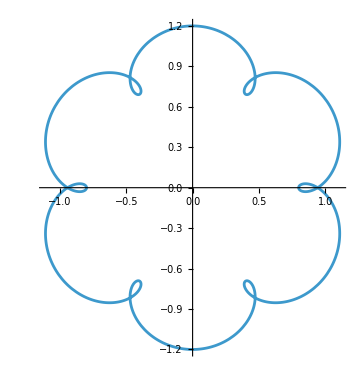

```mathematica
ParametricPlot[S9[t,7],{t,0,2Pi}]
```

```mathematica
G9[n_]:=RevolutionPlot3D[{Sin[t]+Sin[n t]/5,Cos[t]+Cos[n t]/5},{t,0,Pi},PlotRange->1.5,PlotPoints->50, Mesh->True]
```

```mathematica
Manipulate[G9[n],{n,1,7,0.5}]
```

```mathematica
(* Rotation by Pi  (half of the surface) *)
```

```mathematica
G9half[n_]:=RevolutionPlot3D[{Sin[t]+Sin[n t]/5,Cos[t]+Cos[n t]/5},{t,0,Pi},{s,0,Pi},PlotRange->1.5,PlotPoints->50, PlotStyle->LightBlue]
```

```mathematica
(* Check *)
```

```mathematica
G9half[3]
```

-Graphics3D-

```mathematica
(* Animate  *)
```

```mathematica
Manipulate[G9half[n],{n,1,7,0.5}]
```

```mathematica
(* If time allows *)
```

```mathematica
(* VectorPlot depicts a vector field defined by a vector  function {vx(x,y),vy(x,y)}. 
Note that v:R2->R2. The plots imitate streamflows fields. The first component corresponds to the x component of the vector field  the second function corresponds to the y component. *)
```

```mathematica
(* Example 1 Depict v[x_,y_]:={x^2,x+y} *)
```

```mathematica
(* Define a vector function *)
```

```mathematica
Clear[v1]
```

```mathematica
v1[x_,y_]:={x^2,x-y^2}
```

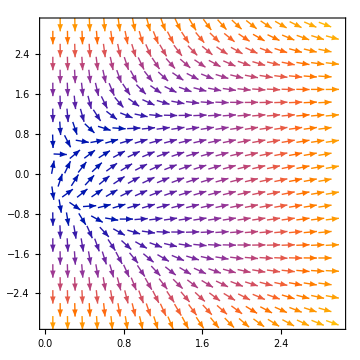

```mathematica
VectorPlot[v1[x,y],{x,0,3},{y,-3,3},VectorPoints->20]
```

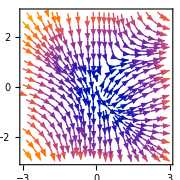

```mathematica
StreamPlot[v1[x,y],{x,-3,3},{y,-3,3},ImageSize->Small]
```

```mathematica
(* Example 2  Create an animation of  a 2D vector field given by 
v2[x_,y_,a_]:={y,-a x}  with regard to a -5,...5. *)
```

```mathematica
Clear[v2]
```

```mathematica
v2[x_,y_,a_]:={y,-a x}
```

```mathematica
(* Check *)
```

```mathematica
v2[1,1,1]
```

{1,-1}

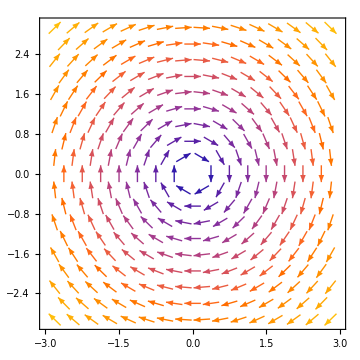

```mathematica
VectorPlot[v2[x,y,1],{x,-3,3},{y,-3,3}]
```

```mathematica
VectorPlot[v2[x,y,1],{x,-3,3},{y,-3,3}]
```

-Graphics-

```mathematica
GV2[a_]:=VectorPlot[v2[x,y,a],{x,-3,3},{y,-3,3}]
```

```mathematica
Manipulate[GV2[a],{a,-5,5,1}]
```

```mathematica
GV2S[a_]:=StreamPlot[v2[x,y,a],{x,-3,3},{y,-3,3}]
```

```mathematica
Manipulate[GV2S[a],{a,-5,5,1}]
```

```mathematica
(* 3D Vector fields *)
```

```mathematica
v3[x_,y_,z_]:={x,y,z}
```

```mathematica
VectorPlot3D[v3[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1},VectorPoints->5,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
VectorPlot3D[v3[x,y,z],{x,-1,1},{y,-1,1},{z,-1,1},VectorPoints->5,PlotLegends->Automatic,VectorMarkers->"Tube"]
```

-Graphics3D-

```mathematica
(* Animate a list of 3D VectorPlots ListV3={{x,y,z},{x,y,-z},{x,-y,-z}}*)
```

```mathematica
ListV3={{x,y,z},{x,y,-z},{x,-y,-z}}
```

{{x,y,z},{x,y,-z},{x,-y,-z}}

```mathematica
G3[i_]:=VectorPlot3D[ListV3[[i]],{x,-1,1},{y,-1,1},{z,-1,1},VectorPoints->5,PlotLegends->Automatic]
```

```mathematica
(* Check *)
```

```mathematica
G3[3]
```

-Graphics3D-

```mathematica
(* Indexed solution G3[i] *)
```

```mathematica
Manipulate[G3[i],{i,1,Length[ListV3],1}]
```

```mathematica
(* List based solution (advanced) *)
```

```mathematica
G3L[L_]:=VectorPlot3D[L,{x,-1,1},{y,-1,1},{z,-1,1},VectorPoints->5,PlotLegends->Automatic]
```

```mathematica
Manipulate[G3L[L],{L, ListV3}]
```

```mathematica
(* ListAnimate improves the speed *)
```

```mathematica
LA3= Table[G3L[L],{L,ListV3}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ListAnimate[LA3,AnimationRunning->False]
```

```mathematica
(* If time allows *)
```

```mathematica
(* Random spheres on the surface R1=0.1,R2=0.2. The surface fz[x_,y_]:=x^2-y^2  *)
```

```mathematica
Clear[f]
```

```mathematica
f[x_,y_]:=x^2-y^2
```

```mathematica
(* Convert f into a parametric surface *)
```

```mathematica
Sf[u_,v_]:={u,v,u^2-v^2}
```

```mathematica
GSf=ParametricPlot3D[Sf[u,v],{u,-1,1},{v,-1,1}]
```

-Graphics3D-

```mathematica
(* Select 2 Random points *)
```

```mathematica
{u1,v1}={RandomReal[{-1,1}],RandomReal[{-1,1}]}
```

{0.0971434,-0.890304}

```mathematica
{u2,v2}={RandomReal[{-1,1}],RandomReal[{-1,1}]}
```

{-0.128931,-0.406375}

```mathematica
R1=0.15
```

0.15

```mathematica
R2=0.25
```

0.25

```mathematica
(* The normal to the parametric surface S(u,v) is given by (∂S)/(∂u)x(∂S)/(∂u)/|(∂S)/(∂u)x(∂S)/(∂u)| ,where x denotes the cross-product (cf. Math3). Mathematica performs symbolic calculations as follows, 
Cross[D[Sf[u,v],u],D[Sf[u,v],v]], where D[f,x] evaluates (∂f)/(∂x).
*)
```

```mathematica
(* -Graphics- *)
```

```mathematica
N1=Cross[D[Sf[u,v],u],D[Sf[u,v],v]]
```

{-2 u,2 v,1}

```mathematica
(* 
Norm[v] evaluates a magnitude of the vector v
*)
```

```mathematica
Norm[N1]
```

√(1+4 Abs[u]^2+4 Abs[v]^2)

```mathematica
(* Cut and paste here  to obtain NV=(∂S)/(∂u)x(∂S)/(∂u)/|(∂S)/(∂u)x(∂S)/(∂u)*)
```

```mathematica
NV[u_,v_]:={-2 u,2 v,1}/√(1+4 Abs[u]^2+4 Abs[v]^2)
```

```mathematica
(* Check *)
```

```mathematica
N1=NV[u1,v1]
```

{-0.0947086,-0.867989,0.487468}

```mathematica
p1=Sf[u1,v1]
```

{0.0971434,-0.890304,-0.783204}

```mathematica
N2=NV[u2,v2]
```

{0.196216,-0.618449,0.760934}

```mathematica
p2=Sf[u2,v2]
```

{-0.128931,-0.406375,-0.148517}

```mathematica
(* 
Nv is the direction vector of a line from p The line equation is then NV t+p, where p is the required point  
*)
```

```mathematica
L1Norm[t_]:=N1*t+p1
```

```mathematica
L2Norm[t_]:=N2*t+p2
```

```mathematica
(* The coordinate of the spheres: *)
```

```mathematica
Center1=L1Norm[R1]
```

{0.0829371,-1.0205,-0.710084}

```mathematica
Center2=L2Norm[R2]
```

{-0.0798771,-0.560987,0.041716}

```mathematica
(* Plot the spheres *)
```

```mathematica
S12=Graphics3D[{{LightGreen,Opacity[0.7],Sphere[Center1,R1]},{LightBlue,Opacity[0.7],Sphere[Center2,R2]}}]
```

-Graphics3D-

```mathematica
(* 
The points are random appearing in different positions on S[u,v]
Since the spheres might be slightly outside the box, PlotRange->1.25 
*)
```

```mathematica
Show[{GSf,S12},PlotRange->1.25]
```

-Graphics3D-